```mathematica
Needs["PlotLegends`"]
MatrixCutFunction[mat_,{t0_,tf_},{T0_,Tf_},thresh_] := Module[{i,j,nmat},
nmat = mat[[t0;;tf,T0;;Tf]];
For[i = 1, i ≤ Length[nmat],i++,
For[j=1,j≤Length[nmat[[1]]],j++,
nmat[[i,j]] = If[nmat[[i,j]]≤ thresh,1,0];
];
];
Return[nmat];
];
PlotGrids[i_,date_,dir_,datdir_,colorfunc1_,colorfunc2_,{t0_,tf_},{T0_,Tf_},thresh_] := Module[{pList,d,dat,p1,p2,p3},
d  = Import[datdir<>date<>"\\"<>dir<>"\\rec"<>i<>".csv"];
p1 = MatrixPlot[d,ColorFunction -> colorfunc1];
p2 = MatrixPlot[d[[t0;;tf,T0;;Tf]],ColorFunction -> colorfunc1];
dat = MatrixCutFunction[d,{t0,tf},{T0,Tf},thresh];
p3 = MatrixPlot[dat,ColorFunction -> colorfunc2];
pList = Position[d[[t0;;tf,T0;;Tf]],_?(#<thresh&)];
Return[{pList,GraphicsGrid[{{p1,p2,p3}}]}];
]
```

```mathematica
dir  = "P62";
datdir = "C:\\Users\\Varchas\\Downloads\\rec\\";
date = "11-27";
```

```mathematica
data1 = PlotGrids["1",date,dir,datdir,"BlueGreenYellow","Monochrome",{1,50},{150,200},0.03];
Show[data1[[2]]]
data1[[1]]
```

-Graphics-

{{21,23},{22,23},{23,23}}

```mathematica
data2 = PlotGrids["2",date,dir,datdir,"BlueGreenYellow","Monochrome",{150,201},{1,50},0.03];
Show[data2[[2]]]
data2[[1]]
```

-Graphics-

{{15,32},{25,46},{26,45},{26,46},{27,45},{27,46},{28,46},{29,46}}

```mathematica
data3 = PlotGrids["3",date,dir,datdir,"BlueGreenYellow","Monochrome",{150,201},{1,50},0.028];
Show[data3[[2]]]
data3[[1]]
```

-Graphics-

{}

```mathematica
data4 = PlotGrids["4",date,dir,datdir,"BlueGreenYellow","Monochrome",{150,201},{1,50},0.028];
Show[data4[[2]]]
data4[[1]];
```

-Graphics-

```mathematica
data5 = PlotGrids["5",date,dir,datdir,"BlueGreenYellow","Monochrome",{150,201},{1,50},0.028];
Show[data5[[2]]]
data5[[1]];
```

-Graphics-

```mathematica
f[x_] := Transpose[Reverse[x]]
```

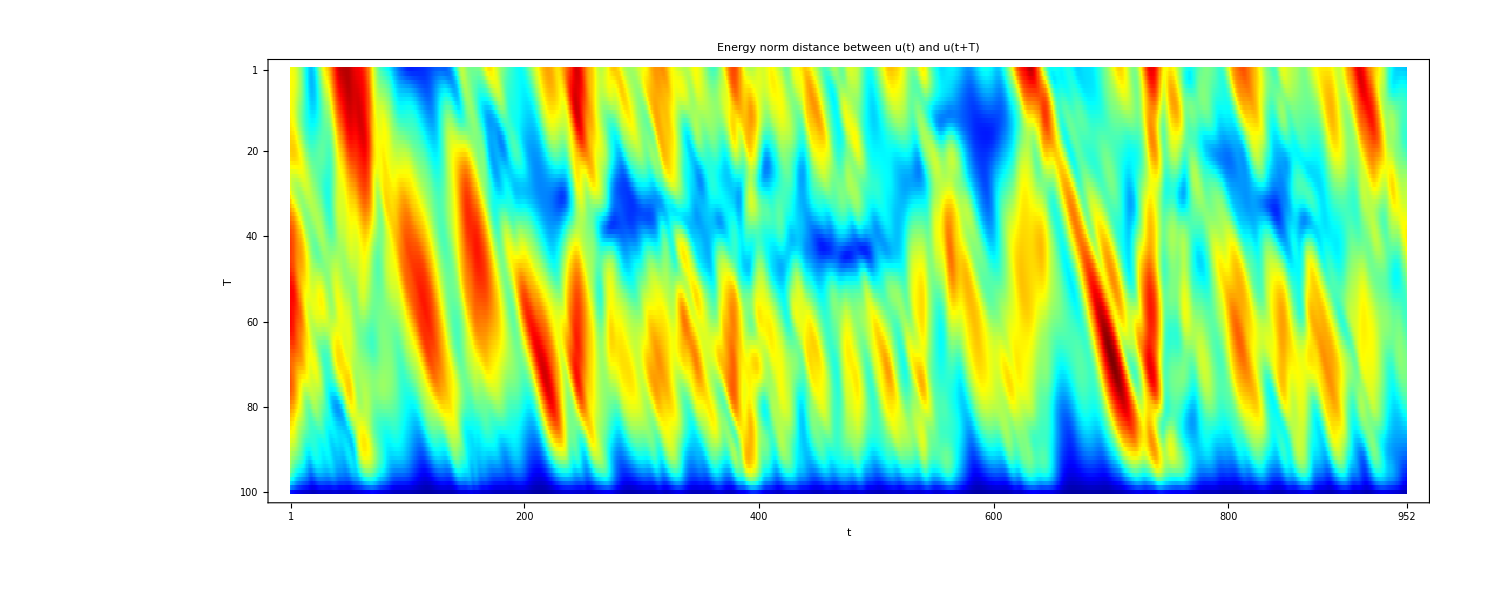

```mathematica
d  = f[f[f[Import[datdir<>"random5.csv"]]]][[1;;,50;;]];
d = d/Max[d];
scale = Table[{i,i},{i,0,Length[d]-1,10}];
scale2 = Table[{Length[d]-1-i,i},{i,0,Length[d]-1,40}];
MatrixPlot[d,FrameLabel -> {Style["T",FontSize -> 20],Style["t",FontSize -> 20],None,None},PlotLabel -> Style["Energy norm distance between u(t) and u(t+T)",FontSize -> 20],ColorFunction ->Function[Blend[RGBColor@@@cMap,Slot[1]]],ColorFunctionScaling -> False]
```

```mathematica
cMap=Partition[ToExpression[StringSplit[Import["C:\\Users\\Varchas\\Desktop\\Reed\\Thesis\\util\\mma\\colormap.txt"]]],3]
```

{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1.},{0,0.0625,1.},{0,0.125,1.},{0,0.1875,1.},{0,0.25,1.},{0,0.3125,1.},{0,0.375,1.},{0,0.4375,1.},{0,0.5,1.},{0,0.5625,1.},{0,0.625,1.},{0,0.6875,1.},{0,0.75,1.},{0,0.8125,1.},{0,0.875,1.},{0,0.9375,1.},{0,1.,1.},{0.0625,1.,0.9375},{0.125,1.,0.875},{0.1875,1.,0.8125},{0.25,1.,0.75},{0.3125,1.,0.6875},{0.375,1.,0.625},{0.4375,1.,0.5625},{0.5,1.,0.5},{0.5625,1.,0.4375},{0.625,1.,0.375},{0.6875,1.,0.3125},{0.75,1.,0.25},{0.8125,1.,0.1875},{0.875,1.,0.125},{0.9375,1.,0.0625},{1.,1.,0},{1.,0.9375,0},{1.,0.875,0},{1.,0.8125,0},{1.,0.75,0},{1.,0.6875,0},{1.,0.625,0},{1.,0.5625,0},{1.,0.5,0},{1.,0.4375,0},{1.,0.375,0},{1.,0.3125,0},{1.,0.25,0},{1.,0.1875,0},{1.,0.125,0},{1.,0.0625,0},{1.,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0},{0.5,0,0}}

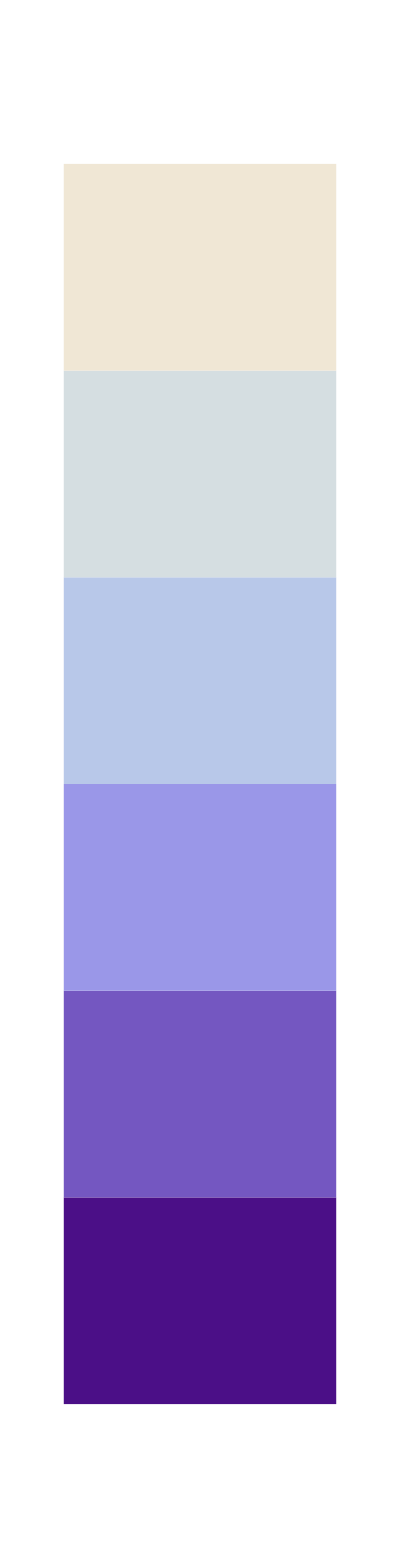

```mathematica
Needs["PlotLegends`"];
myLegend=Graphics[{Legend[ColorData["LakeColors"][1-#1]&,6,"","",LegendShadow->{0.025,-0.025}]},Axes->{True,True},Ticks->{None,Join[Table[{-.21-(.13 k),120-20 k,{0.75,0.},{GrayLevel[0.],AbsoluteThickness[0.25]}},{k,0,6}],Table[{-.21-(.13/4 k),"",{0.0375,0.},{GrayLevel[0.],AbsoluteThickness[0.25]}},{k,0,24}]]},ImagePadding->20]
```